# Import and plot the cross sections for neutrino dissociation of deuteron

## Clean the variables

```mathematica
<<Utilities`CleanSlate`
```

```mathematica
CleanSlate[]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 4 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,URLUtilities`,PacletManager`,System`,Global`}

## Import the .txt files

```mathematica
NuNC = 10^-100 + Import[NotebookDirectory[]<>"NuNC.txt", "Data"]; 
NubarNC = 10^-100 +Import[NotebookDirectory[]<>"NubarNC.txt", "Data"]; 
NuCC =10^-100 + Import[NotebookDirectory[]<>"NuCC.txt", "Data"]; 
NubarCC = 10^-100 +Import[NotebookDirectory[]<>"NubarCC.txt", "Data"];
```

## Generate interpolating functions

```mathematica
fNuNC = Interpolation[NuNC, InterpolationOrder->1];
fNubarNC = Interpolation[NubarNC, InterpolationOrder->1];
fNuCC = Interpolation[NuCC, InterpolationOrder->1];
fNubarCC = Interpolation[NubarCC, InterpolationOrder->1];
```

## Compare with NSGK at 10 MeV

```mathematica
fNuNC[10.] (* NSGK > 1.100 x 10^-42 *)
```

1.107×10^-42

```mathematica
fNubarNC[10.] (*NSGK > 1.047 x 10^-42 *)
```

1.034×10^-42

```mathematica
fNuCC[10.] (* NSGK > 2.686 x 10^-42 *)
```

2.629×10^-42

```mathematica
fNubarCC[10.] (*NSGK > 1.233 x 10^-42 *)
```

1.237×10^-42

The discrepancy is less than 5 %

## Plots : NC - Blue; CC- Red; Neutrino - Solid; Antineutrino - Dashed

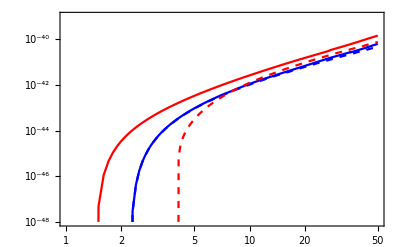

```mathematica
ListLogLogPlot[{NuNC, NubarNC, NuCC, NubarCC}, Joined->True, Frame->True, PlotRange->{{1.,50},{10^-48, 10^-39}},GridLines->Automatic,  
PlotStyle->{Directive[Blue], Directive[Blue, Dashed], Directive[Red], Directive[Red, Dashed]}
 ]
```